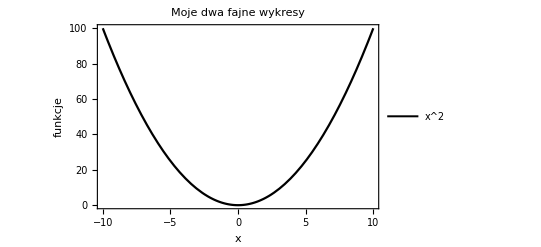

```mathematica
Plot[{x^2},{x,-10,10},Frame->True,FrameLabel->{StyleForm["x ",FontSize->14,Black],StyleForm["funkcje",FontSize->14,Red]},PlotStyle->{{Thickness[0.004],Black},{Thickness[0.004],Dashing[{0.02,0.015}],Black}},PlotLegends->{"x^2"},BaseStyle->{FontFamily->"Aharoni",FontSize->14},ImageSize->Scaled[0.7],PlotLabel->StyleForm["Moje dwa fajne wykresy",FontSize->14,Green]]
```

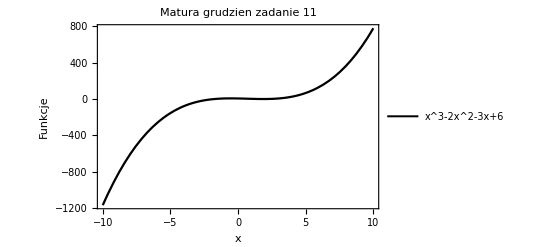

```mathematica
(*x^3-2x^2-3x+6, (x+2)(x^2+3)*)
Plot[{(x^3-2x^2-3x+6)},{x,-10,10},Frame->True,FrameLabel->{StyleForm["x ",FontSize->14,Black],StyleForm["Funkcje",FontSize->14,Red]},PlotStyle->{{Thickness[0.004],Black},{Thickness[0.004],Dashing[{0.02,0.015}],Black}},PlotLegends->{"x^3-2x^2-3x+6"},BaseStyle->{FontFamily->"Aharoni",FontSize->14},ImageSize->Scaled[0.7],PlotLabel->StyleForm["Matura grudzien zadanie 11",FontSize->14,Green]]
```

```mathematica
(*Oblicz całki nieoznaczone*)
(*x^4dx, sinx/3dx, dx/x+3, 3^3xdx, sinx/sqrt(1+2cosx), ... *)
Integrate[x^4,x]
```

x^5/5

```mathematica
∫1/(x+3)ⅆx
```

Log[3+x]

```mathematica
Integrate[Sin[x/3],x]
```

-3 Cos[x/3]

```mathematica
∫E^4xⅆx
```

(ⅇ^4 x^2)/2

```mathematica
Integrate[Sin[x]/Sqrt(1+2*Cos[x]),x]
```

-Cos[x]/Sqrt-Cos[x]^2/Sqrt

```mathematica
∫x^2*Log10ⅆx
```

(Log10 x^3)/3

```mathematica
Integrate[Log10[x]/(x+1)^2,x]
```

(Log[x]-Log[x]/(1+x)-Log[1+x])/Log[10]

```mathematica
∫(4x-3/x^2+3x+4)ⅆx
```

3/x+4 x+(7 x^2)/2

```mathematica
Integrate[Cos[x]/1+Cos[x],x]
```

2 Sin[x]

```mathematica
(*Całki oznaczaona*)
(*x^2, 1/(2x+1)^2, ...*)
Integrate[x^2,{x,-3,3}]
```

18

```mathematica
∫_0^1 1/(2z+1)^3ⅆz
```

2/9

```mathematica
Integrate[Cos[x/2]*Cos[3x/2],{x,0,x}]
```

1/2 (1+Cos[x]) Sin[x]

```mathematica
∫_0^3 (1+Log10[y])^2ⅆy
```

3+(3 (2+Log[3]^2-Log[9]))/Log[10]^2+(2 (-3+Log[27]))/Log[10]

```mathematica
Integrate[x*Sin[x]*Cos[x],{x,-x,x}]
```

1/4 (-2 x Cos[2 x]+Sin[2 x])

```mathematica
(*Granice*)
(*lim x->0 sin4x/sin3x*)
 Limit[Sin[4x]/Sin[3x],x->0]
```

4/3

```mathematica
Limit[(1+1/n)^n,n->0]
```

1

```mathematica
Limit[(Tan^2)[2x]/(Sin^2)[x/3],x->0]
```

Limit[(Tan^2[2 x])/(Sin^2[x/3]),x→0]

```mathematica
Limit[Sqrt[3x]/x,x->0]
```

∞

```mathematica
Limit[(3x^2-1)/(5x^2+2x),x->0]
```

-∞